Robotic Arm Control Using Large Language Models

Curran Flanders

-Graphics-

The use of large language models (LLMs) can add natural language comprehension and reasoning abilities to a robot control system.  This project uses the capabilities of large language models to enable a robotic arm to follow natural language instructions. The arm is simulated in Mathematica in an environment containing other objects. First, a 2D model of the arm is constructed. Then, the arm is extended into 3D.  Functionality is added to allow the arm to be used in different environments. Each environment contains a collection of 3D objects. Finally, functionality is added to allow the LLM to guide the movement of the arm by specifying a list of sequential target positions.

## Implementing an LLM Controlled Robot Arm in Mathematica

The purpose of this project is to create a workflow and code that allows a user to control a simulated robot arm with natural language instructions. The natural language instructions will be passed to a large language model (LLM) which will interpret the instructions and determine the positions to which the arm will be moved. The LLM specifies points in space for the arm to move to, but the inverse kinematics must be handled in a separate process.

The inputs to the LLM are a prompt from the user, a string description of the arm’s environment, and a template string to enclose this data. The LLM returns a path of points whose trajectory the arm should follow. Inverse kinematics is used to determine the joint angles the robot arm must have to reach these positions. An interpolation function is created between the sets of joint angles corresponding to the points along the path. This leads to a continuous path between the sets of points.  A graphic showing the arm travelling along its path is displayed.

This process should work in a similar manner for any LLM whose API is directly accessible by Wolfram, but testing has been performed exclusively with GPT-4 by OpenAI.

### 2D Kinematics

The 2D model of the robot arm, which we will extend to the 3D case, has two degrees of freedom. The angle between the base and the arm’s first segment will be referred to as θ1. The angles between the first and second segment and the angle between the second and third segment are identical and referred to as θ2.  If  the length of each segment is 1, the position of the hand in terms of the joint angles is as follows.

x = (1+2cos(θ2))cos(θ1+θ2)   
y = (1+2cos(θ2))sin(θ1+θ2) 

The analysis of robotic arms involves both forward kinematics and inverse kinematics. A robot arm has a number of degrees of freedom, each of which is a variable that typically specifies an arm segment’s angular position around an axis or the angle that it forms with another segment. These degrees of freedom can be specified as a set of angles that together completely describe the arm’s position at a given time. Forward kinematics is the process of using these joint angles to find the position of the robot’s hand. Inverse kinematics is the opposite procedure, finding the joint angles from the position of the hand. Although forward kinematics is a function such that every input is mapped to a unique output, inverse kinematics is not a function since there may be multiple possible sets of angles that map to a given position.

#### 2D Forward Kinematics

Determine the point  in 2D that the robot’s hand reaches when its arm joints are bent at specified angles:

```mathematica
ClearAll[robotArmForwardKinematics2D]
robotArmForwardKinematics2D[θ1_?NumericQ,θ2_?NumericQ]:=With[{base={0,0}},
	RotationTransform[θ1,base][{1,0}]+RotationTransform[θ1+θ2,base][{1,0}]+RotationTransform[θ1+2θ2,base][{1,0}]]
```

#### 2D Inverse Kinematics

Determine the angles at which the arm’s joints must bend in order for its hand to reach a specific point specified with 2D Cartesian coordinates:

```mathematica
ClearAll[robotArmInverseKinematics2D]
robotArmInverseKinematics2D[{x_?NumericQ,y_?NumericQ}]:=(NSolve[{
	RotationTransform[θ1,{0,0}][{1,0}]+RotationTransform[θ1+θ2,{0,0}][{1,0}]+RotationTransform[θ1+2θ2,{0,0}][{1,0}]=={x,y},
	0<=θ1<=π,-π/2<=θ2<=0},{θ1,θ2}]//If[Length[#]>0&&y>=0,Values[First[#]],Failure["PositionUnreachable","MessageTemplate"->"This point is unreachable."]]&)
```

#### 2D Graphics

Make a visual representation of the 2D cross section of the arm at specified joint angles:

```mathematica
ClearAll[robotArmAnglePlot2D]
robotArmAnglePlot2D[{θ1_,θ2_}]:=Module[{base={0,0},elbow,elbow2,hand},
	elbow=RotationTransform[θ1,base][{1,0}];
	elbow2=elbow+RotationTransform[θ1+θ2,base][{1,0}];
	hand=elbow2+RotationTransform[θ1+2θ2,base][{1,0}];
	Graphics[{Circle[],Line[{base-{2,0},base+{2,0}}],Arrow[{base,elbow}],Arrow[{elbow,elbow2}],Arrow[{elbow2,hand}]}]];
```

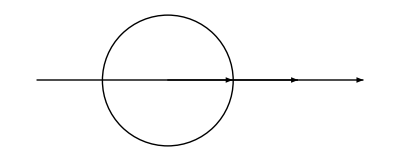
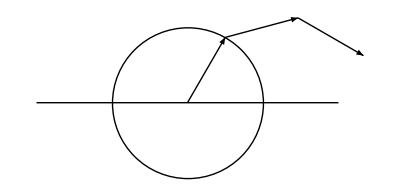

```mathematica
Row[{robotArmAnglePlot2D[{0,0}],robotArmAnglePlot2D[{π/3,-π/4}]}]
```

Make  a  visual  representation  of  the  2D  cross  section  of  the  arm  with  joint  angles  automatically  calculated  such  that  the  hand  reaches  a  specified  set of (x,y) coordinates:

```mathematica
ClearAll[robotArmPositionPlot2D]
robotArmPositionPlot2D[handCoords_List]:=Module[{θ1,θ2,base={0,0},elbow,elbow2,hand},If[FailureQ[#],#,
	{θ1,θ2}=#;
	elbow=RotationTransform[θ1,base][{1,0}];
	elbow2=elbow+RotationTransform[θ1+θ2,base][{1,0}];
	hand=elbow2+RotationTransform[θ1+2θ2,base][{1,0}];
	Graphics[{Circle[],Line[{base-{2,0},base+{2,0}}],Arrow[{base,elbow}],Arrow[{elbow,elbow2}],Arrow[{elbow2,hand}]}]]&@robotArmInverseKinematics2D[handCoords]];
```

### 3D Kinematics and Graphics

To extend this model into the third dimension, we define an additional angle, swivelθ. This variable represents the rotation of the arm around the axis that is perpendicular to the arm’s base and passes through the center of the base. The 3D model can be visualized as follows.

-Graphics-

This leads us to the 3D extension of the equations described in the section on 2D kinematics.

x = (1+2Cos(θ2))(Cos(θ1+θ2))Cos(swivelθ)
y = (1+2Cos(θ2))(Cos(θ1+θ2))Sin(swivelθ))
z = (1+2Cos(θ2))Sin(θ1+θ2)

#### 3D Forward Kinematics

Determine the location of the robot’s hand given its joint angles:

```mathematica
ClearAll[robotArmForwardKinematics3D]
robotArmForwardKinematics3D[swivelθ_?NumericQ,θ1_?NumericQ,θ2_?NumericQ]:=RotationTransform[swivelθ,{0,0,1}][Insert[robotArmForwardKinematics2D[θ1,θ2],0,2]]
```

#### 3D Inverse Kinematics

Determine a set of joint angles that will cause the robot’s hand to reach the specified position:

```mathematica
ClearAll[robotArmInverseKinematics3D]
robotArmInverseKinematics3D[{x_?NumericQ,y_?NumericQ,z_?NumericQ}]:=Module[{swivelθ},
	swivelθ=If[x>0,ArcTan[y/x],ArcTan[y/x]+π];
	swivelθ=Mod[swivelθ,2π,-π];
	If[FailureQ[#],#,Prepend[#,swivelθ]]&@robotArmInverseKinematics2D@Delete[RotationTransform[-swivelθ,{0,0,1}][{x,y,z}],2]
	]
```

#### 3D Graphics

Plot the robot position in 3D given given angle specifications:

```mathematica
ClearAll[robotArmAnglePlot3D]
Options[robotArmAnglePlot3D]={Axes->True,AxesLabel->{"x","y","z"},PlotRange->3.2{{-1,1},{-1,1},{-.01,1}},ImageSize->Medium};
robotArmAnglePlot3D[swivelθ_:0,θ1_:0,θ2_:0,OptionsPattern[]]:=Module[{base={0,0,0},swivelVector,swivelVectorNormal,elbow,elbow2,hand},
	swivelVector=Append[AngleVector[swivelθ],0];
	swivelVectorNormal=Append[AngleVector[swivelθ-π/2],0];
	elbow=RotationTransform[θ1,swivelVectorNormal][swivelVector];
	elbow2=elbow+RotationTransform[θ1+θ2,swivelVectorNormal][swivelVector];
	hand=elbow2+RotationTransform[θ1+2θ2,swivelVectorNormal][swivelVector];
	Graphics3D[{
		(*Robot base: (lazy zusan)*)
		FaceForm[Opacity[.1]],Cylinder[{base,base+{0,0,.2}},1],Dashed,Arrow[{base,swivelVector}],Dashing[None],
		(*Robot upper arm:*)
		Blue,Cylinder[{base,elbow},.1],
		(*Robot middle arm:*)
		Cylinder[{elbow,elbow2},.1],
		(*Robot lower arm:*)
		Cylinder[{elbow2,hand},.1],
		(*Robot hand:*)
		Ball[hand,.2]},
		Axes->OptionValue[Axes],AxesLabel->OptionValue[AxesLabel],
		PlotRange->OptionValue[PlotRange],ImageSize->OptionValue[ImageSize]]]
```

```mathematica
robotArmAnglePlot3D@@robotArmInverseKinematics3D@First[randomRobotGoalPositions[1]]
```

-Graphics3D-

Creates a simple 3D graphic of the robot arm with the hand at specified Cartesian coordinates:

```mathematica
ClearAll[robotArmPositionPlot3D]
Options[robotArmPositionPlot3D]={Axes->True,AxesLabel->{"x","y","z"},PlotRange->3.2{{-1,1},{-1,1},{-.01,1}},ImageSize->Medium};
robotArmPositionPlot3D[handCoords_List,OptionsPattern[]]:=Module[{swivelθ,θ1,θ2,base={0,0,0},swivelVector,swivelVectorNormal,elbow,elbow2,hand},If[FailureQ[#],#,
	{swivelθ,θ1,θ2}=#;
	swivelVector=Append[AngleVector[swivelθ],0];
	swivelVectorNormal=Append[AngleVector[swivelθ-π/2],0];
	elbow=RotationTransform[θ1,swivelVectorNormal][swivelVector];
	elbow2=elbow+RotationTransform[θ1+θ2,swivelVectorNormal][swivelVector];
	hand=elbow2+RotationTransform[θ1+2θ2,swivelVectorNormal][swivelVector];
	Graphics3D[{
		(*Robot base: (lazy zusan)*)
		FaceForm[Opacity[.1]],Cylinder[{base,base+{0,0,.2}},1],Dashed,Arrow[{base,swivelVector}],Dashing[None],
		(*Robot upper arm:*)
		Blue,Cylinder[{base,elbow},.1],
		(*Robot middle arm:*)
		Cylinder[{elbow,elbow2},.1],
		(*Robot lower arm:*)
		Cylinder[{elbow2,hand},.1],
		(*Robot hand:*)
		Ball[hand,.2]},
		Axes->OptionValue[Axes],AxesLabel->OptionValue[AxesLabel],
		PlotRange->OptionValue[PlotRange],ImageSize->OptionValue[ImageSize]]]]&@robotArmInverseKinematics3D[handCoords]
```

This shows the robot arm moving to a valid position.

```mathematica
robotArmPositionPlot3D[{2.0391310416650805, 0., 0.41335232586276466}]
```

-Graphics3D-

This demonstrates how errors are caught if an invalid position is entered.

```mathematica
(*The angle in the argument is not reachable*)
robotArmPositionPlot3D[{2.0391310416650805,0.,-1},PlotRange->All]
```

Failure[…]

#### Plotting a path for the arm in 3D

Converts a discrete list of target positions, specified by the arm’s joint angles, to a continuous function that outputs joint angles for any point along the arm’s path:

```mathematica
ClearAll[getRobotArmMovementFunction]
(*The function takes a list of lists of {{swivelθ,θ1,θ2},{...},...}*)
getRobotArmMovementFunction[angleSpecs_List]:=Interpolation[#,InterpolationOrder->1]&@MapIndexed[{First[#2],#1}&,angleSpecs]
```

Generates a list of random 3D points on the ground that are reachable by the arm:

```mathematica
ClearAll[randomRobotGoalPositions]
randomRobotGoalPositions[n_Integer]:=
	RotationTransform[RandomReal[{-π,π}],{0,0,1}]/@(Append[#,0]&/@RandomPoint[Annulus[{0,0},{1,3}],n])
```

### Defining the Environment

We  will  define  each environments  for  the  arm  as  a dataset that includes three columns: position, descriptions, and geometry. The LLM will receive the position and description of each object from the prompt. The geometry will be used to visualize the object in 3D.

#### Creating Environment Datasets

Generate roughly equally spaced positions for objects in the environment:

```mathematica
ClearAll[precomputedPositions]
precomputedPositions[n_Integer]:=With[{swivelθ=RandomReal[{-π,π}]},
	RotationTransform[swivelθ,{0,0,1}]/@(Append[#,0]&/@(RandomPoint[Annulus[{0,0},{1,3}],n]))]/;n<=3
precomputedPositions[n_Integer]:=With[{swivelθ=RandomReal[{-π,π}]},
	RotationTransform[swivelθ,{0,0,1}]/@(Append[#,0]&/@([[n-3]]))]/;3<n<=26
```

```mathematica
Graphics3D[Point[precomputedPositions[26]],ImageSize->Tiny]
```

-Graphics3D-

Helper function: Translate 3D objects:

```mathematica
ClearAll[translate3DObject]
translate3DObject[object_Graphics3D,vect_List:{0,0,0}]:=First[MapAt[
	TranslationTransform[vect],object,Map[Append[#,1]&,Position[object,_GraphicsComplex]]]]
	
translate3DObject[object_List,vect_List:{0,0,0}]:=translate3DObject[Graphics3D[object],vect]
```

Helper function: Scale 3D objects:

```mathematica
ClearAll[scale3DObject]
scale3DObject[object_Graphics3D,s_:1,p_List:{0,0,0}]:=First[MapAt[
	ScalingTransform[{s,s,s},p],object,Map[Join[#,{1}]&,Position[object,_GraphicsComplex]]]]

scale3DObject[object_List,s_:1,p_List:{0,0,0}]:=scale3DObject[Graphics3D[object],s,p]
```

Get a 3D object’s dimensions:

```mathematica
ClearAll[get3DObjectDimensions]
get3DObjectDimensions[object_]:=Abs[Subtract@@@Transpose[CoordinateBoundingBox[
	Flatten[Cases[object,g_GraphicsComplex:>First[g],∞],1]]]]
```

Get the centroid of the base a 3D object:

```mathematica
ClearAll[get3DObjectBaseCentroid]
get3DObjectBaseCentroid[object_]:=With[{bbox=CoordinateBoundingBox[
	Flatten[Cases[object,g_GraphicsComplex:>First[g],∞],1]]},
	Append[Mean[bbox[[All,{1,2}]]],bbox[[1,3]]]]
```

Center the base of a 3D object at the origin, and scale it so it’s largest dimension is equal to length:

```mathematica
ClearAll[standardize3DObject]
standardize3DObject[object_,length_:1]:=(translate3DObject[#,-get3DObjectBaseCentroid[#]]&@
	scale3DObject[object,length/Max[get3DObjectDimensions[object]]])
```

An example environment is generated here. It uses objects from the built-in Geometry3D data.

Define some example objects to include in the robot’s environment:

```mathematica
ClearAll[standardizedExampleObjects]
standardizedExampleObjects=Graphics3D[#,Axes->True]&/@standardize3DObject/@ExampleData/@ExampleData["Geometry3D"];
```

Associate each object with a description:

```mathematica
objectsWithDescriptions = Thread[{
    	{"Bass Guitar", "Beethoven", "Castle Wall", "Cone", "Cow", "Deimos", "Galleon", "Hammerhead Shark",
     		"Horse", "Klein Bottle", "Moebius Strip", "Phobos", "Potted Plant", "Seashell", "Sedan Car",
     		"Space Shuttle", "Stanford Bunny", "Torus", "Tree", "Triceratops", "Tugboat", "Utah Teapot",
     		"Utah VW Bug", "Vase", "Viking Lander", "Wrench", "Zeppelin"},
    		standardizedExampleObjects}];
```

Generate an environment with n objects for the LLM+Arm system:

```mathematica
ClearAll[generateArmEnvironment]
generateArmEnvironment[n_]:=Module[{pos=precomputedPositions[n],obj=RandomSample[objectsWithDescriptions,n],env},
	env=Transpose@Dataset[AssociationThread[
		{"Position","Description","Geometry"},
		Transpose[Join@@@Thread[{List/@pos,obj}]]]];
	env[All,<|#,"Geometry"->Graphics3D@translate3DObject[#Geometry,#Position]|>&]]
```

```mathematica
exampleEnv=generateArmEnvironment[4]
```

Dataset[<>]

#### Accessing Data from an Environment Dataset

Retrieve geometry from the environment for visualizations:

```mathematica
ClearAll[environmentGeometry]
environmentGeometry[env_Dataset]:=First/@Normal[env[All,"Geometry"]]
```

Retrieve information from the environment for the LLM:

```mathematica
ClearAll[describeEnvironment]
describeEnvironment[env_Dataset]:=Normal[env[All,{"Position","Description"}]]
```

#### Graphing the Robot Arm in 3D with an Environment

Plots the robot arm in its environment:

```mathematica
ClearAll[robotArmPlot3D]
Options[robotArmPlot3D]={PlotRange->3.2{{-1,1},{-1,1},{-.01,1}}};
robotArmPlot3D[handAngles_List:{1,1,1},environment_Dataset:Dataset[{}]]:=Module[{swivelθ,θ1,θ2,base={0,0,0},swivelVector,swivelVectorNormal,elbow,elbow2,hand},
	{swivelθ,θ1,θ2}=handAngles;
	swivelVector=Append[AngleVector[swivelθ],0];
	swivelVectorNormal=Append[AngleVector[swivelθ-π/2],0];
	elbow=RotationTransform[θ1,swivelVectorNormal][swivelVector];
	elbow2=elbow+RotationTransform[θ1+θ2,swivelVectorNormal][swivelVector];
	hand=elbow2+RotationTransform[θ1+2θ2,swivelVectorNormal][swivelVector];
		Graphics3D[{
		(*Robot base: (lazy zusan)*)
		FaceForm[Opacity[1]],{MaterialShading["Silver"],Cylinder[{base,base+{0,0,.2}},0.2],
		(*Robot upper arm:*)
		LightGray,Cylinder[{base,elbow},.1],
		(*Robot middle arm:*)
		Cylinder[{elbow,elbow2},.1],
		(*Robot lower arm:*)
		Cylinder[{elbow2,hand},.1],
		(*Robot hand:*)
		Ball[hand,.2]},
		environmentGeometry[environment]}, 
		Axes->True,AxesLabel->{"x","y","z"},PlotRange->All,ImageSize->500]]
```

```mathematica
robotArmPlot3D[{1,1,1},exampleEnv]
```

-Graphics3D-

### Controlling the Arm with an LLM

We  desire  for  the  LLM  to  provide  coordinate  points  for  the  arm  to  travel  to  sequentially. The prompt uses an identical prompt template for each command. The template is modified by adding the environment of the arm and the user’s instructions. However, the LLM cannot accept the environment objects directly as 3D graphics objects due to maximum prompt size. For detailed objects, especially those imported from 3D object files, this might overwhelm the maximum number of tokens in the prompt and provide data that is not understandable to the LLM.

A template for a prompt that will instruct the LLM to return a list of points for the arm to move to in sequence:

```mathematica
templateLLMPrompt=LLMFunction["You are a control system tasked with instructing a robot arm in a 3D environment. To instruct the arm, give it a list of 
successive {x,y,z} coordinates (where z is height) to perform the specified task which will follow at the end of this instruction set. The list should be 
in the format {position1,position2,position3,...}. Example: {{1,2,3},{4,5,6}} . Do not wrap the output in an additional list, there should only be a single 
list containing one sublist for each coordinate. Return only this list of coordinates and nothing else.\n\nA description of your environment as well as your 
task instructions will follow:\n\nENVIRONMENT DESCRIPTION:`1`\n\nTASK INSTRUCTIONS:`2`"];
```

Informs the LLM of the arm’s environment and its natural language instructions and returns the raw LLM output:

```mathematica
ClearAll[getLLMControlList]
getLLMControlList[prompt_,environment_]:=templateLLMPrompt[environment,prompt]
```

Creates an animation of the arm’s joint angles moving between a list of specified values, changing the position of the hand:

```mathematica
ClearAll[robotArmAnimate3D]
robotArmAnimate3D[angles_List,environment_Dataset]:=Module[{pathFunction},
	If[Length[angles]==1,robotArmPlot3D[angles[[1]],environment], pathFunction=getRobotArmMovementFunction[angles];
	Animate[robotArmPlot3D[pathFunction[x],environment],{x,1,Length[angles]},AnimationRepetitions->1,AnimationRunning->False]]]
```

Simulates the robot arm following natural language instructions from the user in a specified environment:

```mathematica
ClearAll[simulateLLMCommands]
simulateLLMCommands[prompt_String,environment_Dataset]:=
	Module[{angles,pathFunction},
angles=Riffle[#,#]&@(robotArmInverseKinematics3D/@Prepend[ToExpression[getLLMControlList[describeEnvironment[environment],prompt]],
{1,1,1}])]
```

## Demonstrations and Testing

GPT-4 was used for this project’s tests.

The arm was successfully able to perform the most basic task, touching all objects in the environment.

```mathematica
robotArmAnimate3D[simulateLLMCommands["Touch all four objects",exampleEnv],exampleEnv]
```

However, when we request that it select only a specific type of object, it initially failed to do so. An example of this follows.

```mathematica
robotArmAnimate3D[simulateLLMCommands["Touch the animals",exampleEnv],exampleEnv]
```

Making it clearer that objects not fitting the specification should be excluded from the analysis resolved this issue.

```mathematica
robotArmAnimate3D[simulateLLMCommands["Touch only the animals",exampleEnv],exampleEnv]
```

When prompted to select an object of a specific color, the arm was able to recognize the correct object despite color not being present in the graphics component of the simulation.

```mathematica
robotArmAnimate3D[simulateLLMCommands["Touch something green",exampleEnv],exampleEnv]
```

The LLM could generate its own prompts to simulate the user’s commands. It favored generating prompts that commanded the arm to touch the objects in a specific sequence. The LLM’s instructions to the arm were correct regardless of whether the environment was sparse (5 objects) or relatively dense (15 objects).

```mathematica
{sparseEnv,mediumDensityEnv,denseEnv}=Table[generateArmEnvironment[i],{i,5,15,5}];

robotArmPlot3D[{1,1,1},mediumDensityEnv]
```

```mathematica
testPrompts=LLMFunction["Generate a set of instructions for a robot arm to perform based on the following environment description. Do not tell the robot arm to pick up or move any of the objects. Only tell them to touch the objects according to your choice of criteria. The environment description follows. It contains object descriptions. Please provide simple natural language instructions, as you would to a human being. \n\n`1`",InsertionFunction->TextString][#]&/@(describeEnvironment[#][[All,"Description"]]&/@{sparseEnv,mediumDensityEnv,denseEnv,veryDenseEnv});
```

```mathematica
test1Instructions=testPrompts[[1]]
```

1. Touch the Galleon.
2. Touch the Sedan Car.
3. Touch the Wrench.
4. Touch the Cone.
5. Touch the Bass Guitar.

```mathematica
test1Animation=robotArmAnimate3D[simulateLLMCommands[testPrompts[[1]],sparseEnv],sparseEnv]
```

```mathematica
test2Instructions=testPrompts[[2]]
```

1. Touch the Horse.
2. Touch the Seashell.
3. Touch the Cone.
4. Touch the Space Shuttle.
5. Touch the Beethoven statue.
6. Touch the Utah Teapot.
7. Touch the Vase.
8. Touch the Zeppelin.
9. Touch the Triceratops.
10. Touch the Castle Wall.

```mathematica
test2Animation=robotArmAnimate3D[simulateLLMCommands[testPrompts[[2]],mediumDensityEnv],mediumDensityEnv]
```

```mathematica
test3Instructions=testPrompts[[3]]
```

1. Touch the Beethoven statue.
2. Touch the Castle Wall.
3. Touch the Tugboat.
4. Touch the Zeppelin.
5. Touch Deimos.
6. Touch the Viking Lander.
7. Touch the Galleon.
8. Touch the Moebius Strip.
9. Touch the Tree.
10. Touch the Triceratops.
11. Touch the Stanford Bunny.
12. Touch the Wrench.
13. Touch the Bass Guitar.
14. Touch the Seashell.
15. Touch the Hammerhead Shark.

```mathematica
test3Animation=robotArmAnimate3D[simulateLLMCommands[testPrompts[[3]],denseEnv],denseEnv]
```

## Concluding Remarks

In this project I have created a basic model of a robotic arm that can be controlled by an LLM. It can serve as a novel proof of concept of an LLM’s ability to identify characteristics of objects and control a simulated physical system in response to natural language prompting.

The LLM was able to identify objects in the environment by their properties, such as color. However, it sometimes defaulted to touching all objects in the environment rather than the ones specified in the prompt unless a keyword such as “only” was used. It was able to perform instructions sequentially and functioned in both sparse environments where there were few objects in reach and dense environments where there were many. The testing process could be partially automated by allowing the LLM itself to invent prompts. However, its imagination in inventing prompts was somewhat limited in this test.

Future work for this project is likely to include a mechanism to allow the arm to move objects within its environment. More robust prompting of the LLM  and handling of its output to allow the arm to perform actions other than moving to the locations of specified objects is another goal. Further experimentation on the LLM prompt templates could provide insight into which behaviors of the LLM are prompt specific and which are inherent to the model. Finally, implementing the LLM control pipeline in Wolfram System Modeller would allow for more realistic object dynamics.

## Acknowledgments

I would like to thank the Wolfram Summer School staff and students who provided advice and assistance to me throughout the project.

My  mentors  Phileas  Dazeley-Gaist  and  Alejandra  Ortiz for  assistance  throughout  the  project  on  planning  and  implementation

Glen  Halley  and  Ankit  Naik  for  offering  assistance  with  Wolfram  System  Modeller

Jofre  Espigule  for  providing  reference  materials

Dr. Stephen  Wolfram  for  high-level  guidance  on  project  direction

## References

Yamada, Y., Bao, Y., Lampinen, A. K., Kasai, J., & Yildirim, I. (2023). Evaluating spatial understanding of large language models. arXiv preprint arXiv:2310.14540.

Zeng, F., Gan, W., Wang, Y., Liu, N., & Yu, P. S. (2023). Large language models for robotics: A survey. arXiv preprint arXiv:2311.07226.

## Cite This Notebook

“Robotic arm control using large language models”
by Curran Flanders
https://community.wolfram.com/groups/-/m/t/3211121